```mathematica
d=Import[NotebookDirectory[]<>"~log - vortex.txt","Table"];
```

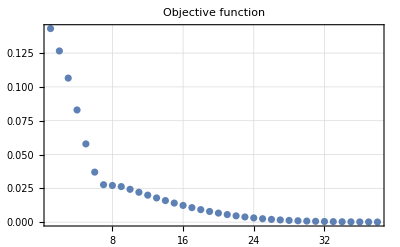

```mathematica
ListPlot[d[[All,2]],PlotTheme->"Detailed",PlotRange->All,PlotLabel->"Objective function"]
```

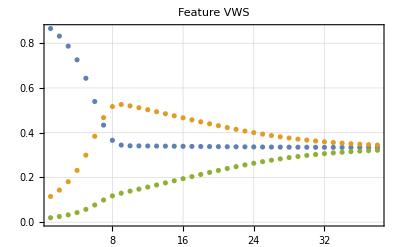

```mathematica
ListPlot[Transpose@d[[All,4;;6]],PlotTheme->"Detailed",PlotRange->All,PlotLabel->"Feature VWS"]
```